### pour charger en memoire

```mathematica
Get[(NotebookDirectory[]<>"2d.data")];
Print[FileByteCount[(NotebookDirectory[]<>"2d.data")]/1024/1024.," Mo"]
```

0.0330896 Mo

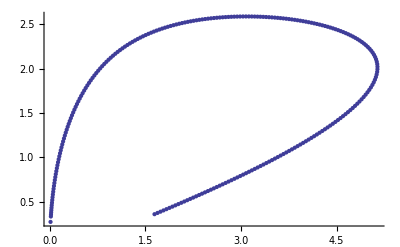

```mathematica
ListPlot[Dataθy02]
```

### pour ecrire sur le disque

```mathematica
DeleteFile[NotebookDirectory[]<>"2d.data"];

Save[NotebookDirectory[]<>"2d.data",{
Dataθy02,Dataθy03,Dataθy05
}];

Print[FileByteCount[(NotebookDirectory[]<>"2d.data")]/1024/1024.," Mo"]
```

0.0330896 Mo